```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
bnTab[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

Arithmetic Functions

## Sum Harmonic Numbers

```mathematica
ClearAll[s,t]
s[n_]:=(Binomial[(n+1)!+n,n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
```

## Highest power of prime p in n!

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
```

```mathematica
f[10,2]
f[10,3]
f[10,5]
f[10,7]
```

8

4

2

1

```mathematica
10!
```

3628800

```mathematica
2^8 3^4 5^2 7
```

3628800

## Moebius Function

### Definition

The Moebius function is defined as follows:
μ(1) = 1;
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
μ(n) = (-1)^k if α_i=1
μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[60]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
10 | 1
12 | 0
15 | 1
20 | 0
30 | -1
60 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,30}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0
13 | -1
14 | 1
15 | 1
16 | 0
17 | -1
18 | 0
19 | -1
20 | 0
21 | 1
22 | 1
23 | -1
24 | 0
25 | 0
26 | 1
27 | 0
28 | 0
29 | -1
30 | -1

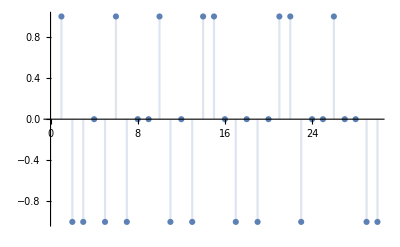

```mathematica
DiscretePlot[MoebiusMu[k],{k,30},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i)

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

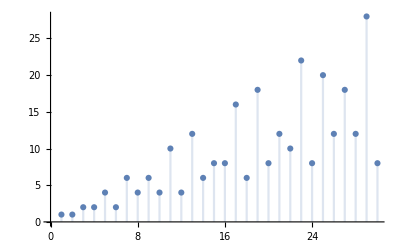

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[MoebiusMu[n],id[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],u[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],n,n,12]
```

4

```mathematica
DirichletConvolve[MoebiusMu[n]^2 EulerPhi[n]^-1,u[n],n,12]
```

3

```mathematica
Table[{k,Log[2,DirichletConvolve[MoebiusMu[n]^2,u[n],n,k]],Total[Map[MoebiusMu[#]^2&,Divisors[k]]],2^PrimeNu[k]},{k,1,10}]//tf
```

1 | 0 | 1 | 1
2 | 1 | 2 | 2
3 | 1 | 2 | 2
4 | 1 | 2 | 2
5 | 1 | 2 | 2
6 | 2 | 4 | 4
7 | 1 | 2 | 2
8 | 1 | 2 | 2
9 | 1 | 2 | 2
10 | 2 | 4 | 4

```mathematica
DirichletConvolve[MoebiusMu[n],Log[n],n,729]//Simplify
```

Log[3]

Numerical Methods and Tools

## Approximate a Sum by an Integral

## Euler-MacLaurin Summation

### Definition / Theorem

#### Example

## Abel Summation

## Stieltjes Integrals

### Definition / Theorem

#### Example

## Slowly oscillating functions

### Definition / Theorem

#### Example

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=Log[Log[x]]
```

```mathematica
Limit[f[5x]/f[x],x->Infinity]
```

1

```mathematica
Limit[(x D[f[x],{x,1}])/f[x],x->Infinity]
```

0

# Notes DSC

Counting

## Definitions

### Definition / Theorem

k-Sequence of I(n)
n-Sharing of I(k)
n-Composition of k

k-Collection of I(n)
n-Partition of I(k)
n-Partition of k

#### Example